```mathematica
Clear["Global`*"]
```

## Figure 2a,b: Changes in niche & fitness differences

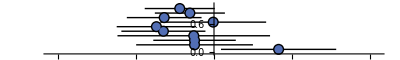

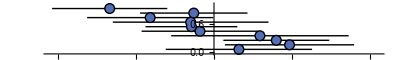

```mathematica
(* Data (S-B, S-P, S-C, S-N, P-B, C-B, B-N, C-P, P-N, C-N; dominant competitor listed first) *)
(* Change in niche differences (x-coordinate: difference, y-coordinate: stacked points) *)
NDdata={{-0.44±0.45,0.95},{-0.31±0.45,0.85},{-0.64±0.48,0.75},{-0.01±0.68,0.65},{-0.74±0.51,0.55},{-0.65±0.54,0.45},{-0.26±0.98,0.35},{-0.25±0.53,0.25},{-0.25±0.75,0.15},{0.83±0.74,0.05}};
(* Change in fitness differences (x-coordinate: difference, y-coordinate: stacked points) *)
FDdata={{-1.34±0.74,0.95},{-0.26±0.69,0.85},{-0.82±0.81,0.75},{-0.30±1.00,0.65},{-0.29±0.59,0.55},{-0.18±0.75,0.45},{0.59±1.14,0.35},{0.80±0.68,0.25},{0.97±0.83,0.15},{0.32±0.94,0.05}};

(* Plots *)
(* Change in niche differences *)
fig2a=Show[ListPlot[NDdata,PlotStyle->{Black},AspectRatio->0.15,PlotRange->{{-2.1,2.1},{-0.05,1.05}},AxesOrigin->{0,-0.05},AxesStyle->{Black,Black},Ticks->{Automatic,None},LabelStyle->{Directive[FontSize->12]}],
ListPlot[NDdata,PlotStyle->{Black,PointSize[0.02]},IntervalMarkersStyle->Transparent],ListPlot[NDdata,PlotStyle->{RGBColor[82/255,110/255,180/255],PointSize[0.015]},IntervalMarkersStyle->Transparent]]

(* Change in fitness differences *)
fig2b=Show[ListPlot[FDdata,PlotStyle->{Black},AspectRatio->0.15,PlotRange->{{-2.1,2.1},{-0.05,1.05}},AxesOrigin->{0,-0.05},AxesStyle->{Black,Black},Ticks->{Automatic,None},LabelStyle->{Directive[FontSize->12]}],
ListPlot[FDdata,PlotStyle->{Black,PointSize[0.02]},IntervalMarkersStyle->Transparent],ListPlot[FDdata,PlotStyle->{RGBColor[82/255,110/255,180/255],PointSize[0.015]},IntervalMarkersStyle->Transparent]]
```

```mathematica
Export["Fig2a.eps",fig2a];
Export["Fig2b.eps",fig2b];
```

## Figure 2c: Niche & Fitness Differences

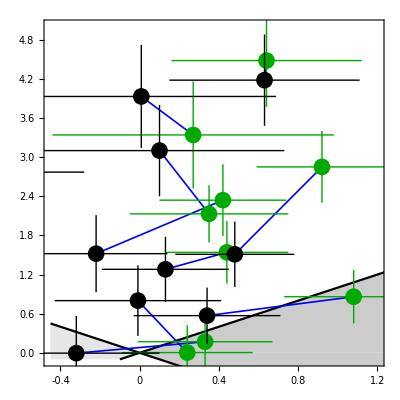

```mathematica
(* Plot parameter space *)
RP=Show[Plot[{-x,x},{x,-0.45,0},Filling->0,FillingStyle->GrayLevel[0.9],PlotStyle->{{Black},{Black}},AxesOrigin->{-0.4,0},PlotRange->{{-0.45,1.2},{-0.1,5}}],Plot[{-x,x},{x,0,1.25},Filling->0,FillingStyle->GrayLevel[0.8],PlotStyle->{{Black},{Black}}],Frame->True,
FrameStyle->{{Black,Black},{Black,Black}},FrameTicks->{{Automatic,None},{{-0.4,0,0.4,0.8,1.2},Automatic}},LabelStyle->Directive[FontSize->20]];

(* Data (niche difference, fitness difference) *)
hand={(*S-B*){0.92±0.33,2.85±0.55},
(*S-P*){0.44±0.31,1.54±0.48},
(*S-C*){0.42±0.32,2.34±0.55},
(*S-N*){0.64±0.48,4.48±0.71},
(*B-P*){1.08±0.35,0.86±0.41},
(*B-C*){0.33±0.34,0.17±0.48},
(*B-N*){0.27±0.71,3.34±0.82},
(*P-C*){0.24±0.33,0.004±0.42},
(*P-N*){0.35±0.40,2.13±0.44},
(*C-N*){-1.74±0.38,2.45±0.48}};
control={(*S-B*){0.48±0.30,1.51±0.50},
(*S-P*){0.13±0.32,1.28±0.50},
(*S-C*){-0.22±0.36,1.52±0.59},
(*S-N*){0.63±0.48,4.18±0.70},
(*B-P*){0.34±0.37,0.57±0.43},
(*B-C*){-0.32±0.42,-0.005±0.57},
(*B-N*){0.008±0.68,3.93±0.79},
(*P-C*){-0.009±0.42,0.80±0.54},
(*P-N*){0.10±0.63,3.10±0.70},
(*C-N*){-0.91±0.63,2.77±0.81}};
(* End points for arrows (must remove SD) *)
hArrow={(*S-B*){0.92,2.85},
(*S-P*){0.44,1.54},
(*S-C*){0.42,2.34},
(*S-N*){0.64,4.48},
(*B-P*){1.08,0.86},
(*B-C*){0.33,0.17},
(*B-N*){0.27,3.34},
(*P-C*){0.24,0.004},
(*P-N*){0.35,2.13},
(*C-N*){-1.74,2.45}};
cArrow={(*S-B*){0.48,1.51},
(*S-P*){0.13,1.28},
(*S-C*){-0.22,1.52},
(*S-N*){0.63,4.18},
(*B-P*){0.34,0.57},
(*B-C*){-0.32,-0.005},
(*B-N*){0.008,3.93},
(*P-C*){-0.009,0.80},
(*P-N*){0.10,3.10},
(*C-N*){-0.91,2.77}};

(* PLOT PARMAETER SPACE, POINTS, AND ARROWS *)
plot=Show[ListLinePlot[{hArrow[[1]],cArrow[[1]]},PlotMarkers->None,PlotStyle->{Blue,Thickness[0.003]}]/.Line->Arrow,
ListLinePlot[{hArrow[[2]],cArrow[[2]]},PlotMarkers->None,PlotStyle->{Blue,Thickness[0.003]}]/.Line->Arrow,
ListLinePlot[{hArrow[[3]],cArrow[[3]]},PlotMarkers->None,PlotStyle->{Blue,Thickness[0.003]}]/.Line->Arrow,
ListLinePlot[{hArrow[[4]],cArrow[[4]]},PlotMarkers->None,PlotStyle->{Blue,Thickness[0.003]}]/.Line->Arrow,
ListLinePlot[{hArrow[[5]],cArrow[[5]]},PlotMarkers->None,PlotStyle->{Blue,Thickness[0.003]}]/.Line->Arrow,
ListLinePlot[{hArrow[[6]],cArrow[[6]]},PlotMarkers->None,PlotStyle->{Blue,Thickness[0.003]}]/.Line->Arrow,
ListLinePlot[{hArrow[[7]],cArrow[[7]]},PlotMarkers->None,PlotStyle->{Blue,Thickness[0.003]}]/.Line->Arrow,
ListLinePlot[{hArrow[[8]],cArrow[[8]]},PlotMarkers->None,PlotStyle->{Blue,Thickness[0.003]}]/.Line->Arrow,
ListLinePlot[{hArrow[[9]],cArrow[[9]]},PlotMarkers->None,PlotStyle->{Blue,Thickness[0.003]}]/.Line->Arrow,ListPlot[hand,PlotStyle->{Darker[Green],PointSize[0.03],Thin}],ListPlot[control,PlotStyle->{Black,PointSize[0.03],Thin}]];
fig2c=Show[RP,plot,AspectRatio->1]
```

```mathematica
Export["Fig2c.eps",fig2c];
```

## Figure 3: Changes in parameters

```mathematica
(* PARAMETERS *)
param={λsC->Around[36500,17300],λbC->Around[4050,1440],λpC->Around[28000,12900],λcC->Around[1060,370],λnC->Around[1530,780],
gs->Around[0.021,0.001],gb->Around[0.038,0.001],gp->Around[0.005,0.0002],gc->Around[0.021,0.001],gn->Around[0.008,0.0004],
ws->0.0017,wb->0.0046,wp->0.0001,wc->0.0036,wn->0.0009,a->4(π 0.2^2),
αssC->Around[2.68,1.52],αsbC->Around[3.74,2.24],αspC->Around[2.97,1.70],αscC->Around[4.92,2.83],αsnC->Around[0.24,0.21],
αbsC->Around[0.46,0.22],αbbC->Around[1.70,0.93],αbpC->Around[0.95,0.44],αbcC->Around[1.52,0.75],αbnC->Around[0.035,0.050],
αpsC->Around[0.45,0.27],αpbC->Around[0.58,0.47],αppC->Around[0.64,0.39],αpcC->Around[2.12,1.30],αpnC->Around[0.063,0.083],
αcsC->Around[0.18,0.10],αcbC->Around[0.43,0.34],αcpC->Around[0.063,0.045],αccC->Around[0.21,0.15],αcnC->Around[0.052,0.065],
αnsC->Around[0.37,0.26],αnbC->Around[5.41,3.55],αnpC->Around[0.95,0.63],αncC->Around[2.78,1.78],αnnC->Around[0.11,0.12],λsH->Around[41500,18800],λbH->Around[4080,1440],λpH->Around[103000,52700],λcH->Around[6140,3040],λnH->Around[5600,3050],
αssH->Around[1.75,0.98],αsbH->Around[0.76,0.54],αspH->Around[2.98,1.65],αscH->Around[1.15,0.70],αsnH->Around[0.13,0.13],
αbsH->Around[0.67,0.31],αbbH->Around[1.83,1.00],αbpH->Around[0.96,0.45],αbcH->Around[0.85,0.45],αbnH->Around[0.033,0.052],
αpsH->Around[0.90,0.56],αpbH->Around[0.81,0.66],αppH->Around[3.68,2.29],αpcH->Around[2.44,1.59],αpnH->Around[0.31,0.25],
αcsH->Around[0.72,0.44],αcbH->Around[1.21,0.92],αcpH->Around[1.01,0.61],αccH->Around[1.09,0.70],αcnH->Around[0.65,0.44],
αnsH->Around[1.08,0.71],αnbH->Around[9.49,6.37],αnpH->Around[1.70,1.15],αncH->Around[15.8,10.7],αnnH->Around[0.29,0.24]};
```

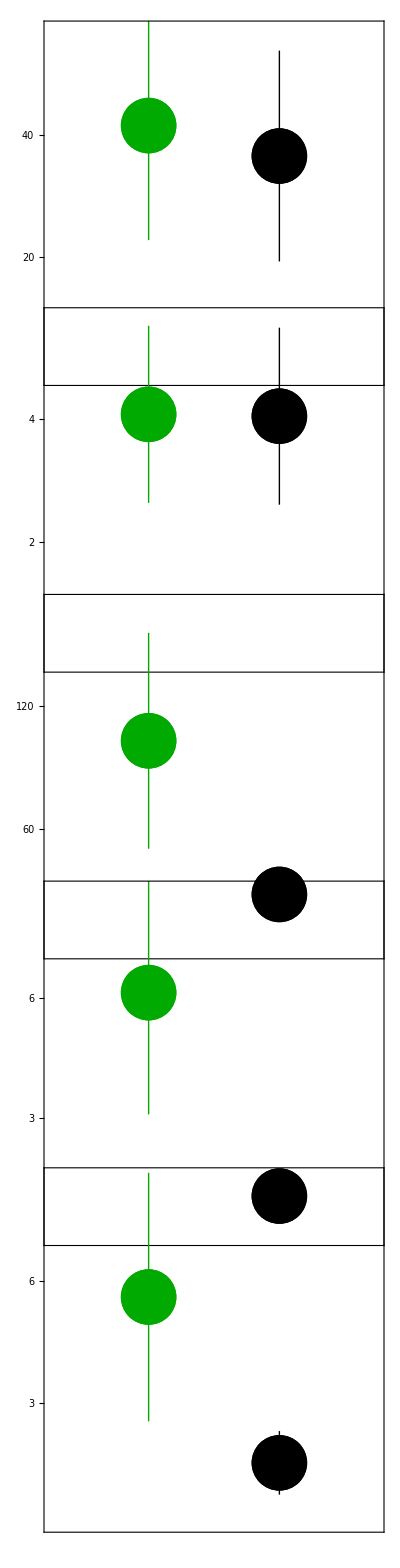

```mathematica
(* LOW-DENSITY GROWTH RATES (Figure 3a) *)
(* (x-coordinates: offset, y-coordinates: parameter means and SE) *)
LDG=GraphicsGrid[{{(* λs *)Show[ListPlot[{{0.15,λsH/1000}}/.param,PlotStyle->{Darker[Green],PointSize[0.1]}],ListPlot[{{0.35,λsC/1000}}/.param,PlotStyle->{Black,PointSize[0.1]}],AspectRatio->2,Frame->True,PlotRange->{{0,0.5},{0,57.5}},FrameStyle->{{Black,Opacity[0]},{Black,Opacity[0]}},FrameTicks->{None,{20,40,{60,"  60"}}},LabelStyle->Directive[FontSize->10]]},
(* λb *){Show[ListPlot[{{0.15,λbH/1000}}/.param,PlotStyle->{Darker[Green],PointSize[0.1]}],ListPlot[{{0.35,λbC/1000}}/.param,PlotStyle->{Black,PointSize[0.1]}],AspectRatio->2,Frame->True,PlotRange->{{0,0.5},{0,5.7}},FrameStyle->{{Black,Opacity[0]},{Black,Opacity[0]}},FrameTicks->{None,{2,4,{6, "    6"}}},LabelStyle->Directive[FontSize->10]]},
(* λp *){Show[ListPlot[{{0.15,λpH/1000}}/.param,PlotStyle->{Darker[Green],PointSize[0.1]}],ListPlot[{{0.35,λpC/1000}}/.param,PlotStyle->{Black,PointSize[0.1]}],AspectRatio->2,Frame->True,PlotRange->{{0,0.5},{0,171}},FrameStyle->{{Black,Opacity[0]},{Black,Opacity[0]}},FrameTicks->{None,{60,120,180}},LabelStyle->Directive[FontSize->10]]},
(* λc *){Show[ListPlot[{{0.15,λcH/1000}}/.param,PlotStyle->{Darker[Green],PointSize[0.1]}],ListPlot[{{0.35,λcC/1000}}/.param,PlotStyle->{Black,PointSize[0.1]}],AspectRatio->2,Frame->True,PlotRange->{{0,0.5},{0,8.75}},FrameStyle->{{Black,Opacity[0]},{Black,Opacity[0]}},FrameTicks->{None,{3,6,{9, "    9"}}},LabelStyle->Directive[FontSize->10]]},
(* λn *){Show[ListPlot[{{0.15,λnH/1000}}/.param,PlotStyle->{Darker[Green],PointSize[0.1]}],ListPlot[{{0.35,λnC/1000}}/.param,PlotStyle->{Black,PointSize[0.1]}],AspectRatio->2,Frame->True,PlotRange->{{0,0.5},{0,8.6}},FrameStyle->{{Black,Opacity[0]},{Black,Opacity[0]}},FrameTicks->{None,{3,6,{9, "    9"}}},LabelStyle->Directive[FontSize->10]]}},Spacings->{0,-230},Alignment->{Center,Center},ImageSize->{UpTo[500],UpTo[600]}]
```

```mathematica
Export["Fig3a.eps",LDG];
```

```mathematica
(* SINAPIS COEFFICIENTS (x-coordinates: offset, y-coordinates: parameter means and SE) *)
yMin=0;yMax=8.55;
sCoef=GraphicsGrid[{{(*S-S*)Show[ListPlot[{{0.15,αssH}}/.param,PlotStyle->{Darker[Green],PointSize[0.1]}],ListPlot[{{0.35,αssC}}/.param,PlotStyle->{Black,PointSize[0.1]}],AspectRatio->2,Frame->True,PlotRange->{{0,0.5},{yMin,yMax}},FrameStyle->{{Black,Opacity[0]},{Black,Opacity[0]}},FrameTicks->{None,{3,6,9}},LabelStyle->Directive[FontSize->10],Prolog->{LightGray,Rectangle[Scaled[{0,0}],Scaled[{1,1}]]}],
(*S-B*)Show[ListPlot[{{0.15,αsbH}}/.param,PlotStyle->{Darker[Green],PointSize[0.1]}],ListPlot[{{0.35,αsbC}}/.param,PlotStyle->{Black,PointSize[0.1]}],AspectRatio->2,Frame->True,PlotRange->{{0,0.5},{yMin,yMax}},FrameStyle->{{Black,Opacity[0]},{Black,Opacity[0]}},FrameTicks->{None,{3,6,9}},LabelStyle->Directive[FontSize->10]],
(*S-P*)Show[ListPlot[{{0.15,αspH}}/.param,PlotStyle->{Darker[Green],PointSize[0.1]}],ListPlot[{{0.35,αspC}}/.param,PlotStyle->{Black,PointSize[0.1]}],AspectRatio->2,Frame->True,PlotRange->{{0,0.5},{yMin,yMax}},FrameStyle->{{Black,Opacity[0]},{Black,Opacity[0]}},FrameTicks->{None,{3,6,9}},LabelStyle->Directive[FontSize->10]],
(*S-C*)Show[ListPlot[{{0.15,αscH}}/.param,PlotStyle->{Darker[Green],PointSize[0.1]}],ListPlot[{{0.35,αscC}}/.param,PlotStyle->{Black,PointSize[0.1]}],AspectRatio->2,Frame->True,PlotRange->{{0,0.5},{yMin,yMax}},FrameStyle->{{Black,Opacity[0]},{Black,Opacity[0]}},FrameTicks->{None,{3,6,9}},LabelStyle->Directive[FontSize->10]],
(*S-N*)Show[ListPlot[{{0.15,αsnH}}/.param,PlotStyle->{Darker[Green],PointSize[0.1]}],ListPlot[{{0.35,αsnC}}/.param,PlotStyle->{Black,PointSize[0.1]}],AspectRatio->2,Frame->True,PlotRange->{{0,0.5},{yMin,yMax}},FrameStyle->{{Black,Opacity[0]},{Black,Opacity[0]}},FrameTicks->{None,{3,6,9}},LabelStyle->Directive[FontSize->10]]
}},Spacings->{115,0},ImageSize->{UpTo[620]}]
```

-Graphics-

```mathematica
(* BUGLOSSOIDES COEFFICIENTS (x-coordinates: offset, y-coordinates: parameter means and SE) *)
yMin=0;yMax=2.85;
bCoef=GraphicsGrid[{{(*B-S*)Show[ListPlot[{{0.15,αbsH}}/.param,PlotStyle->{Darker[Green],PointSize[0.1]}],ListPlot[{{0.35,αbsC}}/.param,PlotStyle->{Black,PointSize[0.1]}],AspectRatio->2,Frame->True,PlotRange->{{0,0.5},{yMin,yMax}},FrameStyle->{{Black,Opacity[0]},{Black,Opacity[0]}},FrameTicks->{None,{1,2,3}},LabelStyle->Directive[FontSize->10]],
(*B-B*)Show[ListPlot[{{0.15,αbbH}}/.param,PlotStyle->{Darker[Green],PointSize[0.1]}],ListPlot[{{0.35,αbbC}}/.param,PlotStyle->{Black,PointSize[0.1]}],AspectRatio->2,Frame->True,PlotRange->{{0,0.5},{yMin,yMax}},FrameStyle->{{Black,Opacity[0]},{Black,Opacity[0]}},FrameTicks->{None,{1,2,3}},LabelStyle->Directive[FontSize->10],Prolog->{LightGray,Rectangle[Scaled[{0,0}],Scaled[{1,1}]]}],
(*B-P*)Show[ListPlot[{{0.15,αbpH}}/.param,PlotStyle->{Darker[Green],PointSize[0.1]}],ListPlot[{{0.35,αbpC}}/.param,PlotStyle->{Black,PointSize[0.1]}],AspectRatio->2,Frame->True,PlotRange->{{0,0.5},{yMin,yMax}},FrameStyle->{{Black,Opacity[0]},{Black,Opacity[0]}},FrameTicks->{None,{1,2,3}},LabelStyle->Directive[FontSize->10]],
(*B-C*)Show[ListPlot[{{0.15,αbcH}}/.param,PlotStyle->{Darker[Green],PointSize[0.1]}],ListPlot[{{0.35,αbcC}}/.param,PlotStyle->{Black,PointSize[0.1]}],AspectRatio->2,Frame->True,PlotRange->{{0,0.5},{yMin,yMax}},FrameStyle->{{Black,Opacity[0]},{Black,Opacity[0]}},FrameTicks->{None,{1,2,3}},LabelStyle->Directive[FontSize->10]],
(*B-N*)Show[ListPlot[{{0.15,αbnH}}/.param,PlotStyle->{Darker[Green],PointSize[0.1]}],ListPlot[{{0.35,αbnC}}/.param,PlotStyle->{Black,PointSize[0.1]}],AspectRatio->2,Frame->True,PlotRange->{{0,0.5},{yMin,yMax}},FrameStyle->{{Black,Opacity[0]},{Black,Opacity[0]}},FrameTicks->{None,{1,2,3}},LabelStyle->Directive[FontSize->10]]
}},Spacings->{115,0},ImageSize->{UpTo[620]}]
```

-Graphics-

```mathematica
(* PAPAVER COEFFICIENTS (x-coordinates: offset, y-coordinates: parameter means and SE) *)
yMin=0;yMax=5.7;
pCoef=GraphicsGrid[{{(*P-S*)Show[ListPlot[{{0.15,αpsH}}/.param,PlotStyle->{Darker[Green],PointSize[0.1]}],ListPlot[{{0.35,αpsC}}/.param,PlotStyle->{Black,PointSize[0.1]}],AspectRatio->2,Frame->True,PlotRange->{{0,0.5},{yMin,yMax}},FrameStyle->{{Black,Opacity[0]},{Black,Opacity[0]}},FrameTicks->{None,{2,4,6}},LabelStyle->Directive[FontSize->10]],
(*P-B*)Show[ListPlot[{{0.15,αpbH}}/.param,PlotStyle->{Darker[Green],PointSize[0.1]}],ListPlot[{{0.35,αpbC}}/.param,PlotStyle->{Black,PointSize[0.1]}],AspectRatio->2,Frame->True,PlotRange->{{0,0.5},{yMin,yMax}},FrameStyle->{{Black,Opacity[0]},{Black,Opacity[0]}},FrameTicks->{None,{2,4,6}},LabelStyle->Directive[FontSize->10]],
(*P-P*)Show[ListPlot[{{0.15,αppH}}/.param,PlotStyle->{Darker[Green],PointSize[0.1]}],ListPlot[{{0.35,αppC}}/.param,PlotStyle->{Black,PointSize[0.1]}],AspectRatio->2,Frame->True,PlotRange->{{0,0.5},{yMin,yMax}},FrameStyle->{{Black,Opacity[0]},{Black,Opacity[0]}},FrameTicks->{None,{2,4,6}},LabelStyle->Directive[FontSize->10],Prolog->{LightGray,Rectangle[Scaled[{0,0}],Scaled[{1,1}]]}],
(*P-C*)Show[ListPlot[{{0.15,αpcH}}/.param,PlotStyle->{Darker[Green],PointSize[0.1]}],ListPlot[{{0.35,αpcC}}/.param,PlotStyle->{Black,PointSize[0.1]}],AspectRatio->2,Frame->True,PlotRange->{{0,0.5},{yMin,yMax}},FrameStyle->{{Black,Opacity[0]},{Black,Opacity[0]}},FrameTicks->{None,{2,4,6}},LabelStyle->Directive[FontSize->10]],
(*P-N*)Show[ListPlot[{{0.15,αpnH}}/.param,PlotStyle->{Darker[Green],PointSize[0.1]}],ListPlot[{{0.35,αpnC}}/.param,PlotStyle->{Black,PointSize[0.1]}],AspectRatio->2,Frame->True,PlotRange->{{0,0.5},{yMin,yMax}},FrameStyle->{{Black,Opacity[0]},{Black,Opacity[0]}},FrameTicks->{None,{2,4,6}},LabelStyle->Directive[FontSize->10]]
}},Spacings->{115,0},ImageSize->{UpTo[620]}]
```

-Graphics-

```mathematica
(* CENTAUREA COEFFICIENTS (x-coordinates: offset, y-coordinates: parameter means and SE) *)
yMin=0;yMax=2.85;
cCoef=GraphicsGrid[{{(*C-S*)Show[ListPlot[{{0.15,αcsH}}/.param,PlotStyle->{Darker[Green],PointSize[0.1]}],ListPlot[{{0.35,αcsC}}/.param,PlotStyle->{Black,PointSize[0.1]}],AspectRatio->2,Frame->True,PlotRange->{{0,0.5},{yMin,yMax}},FrameStyle->{{Black,Opacity[0]},{Black,Opacity[0]}},FrameTicks->{None,{1,2,3}},LabelStyle->Directive[FontSize->10]],
(*C-B*)Show[ListPlot[{{0.15,αcbH}}/.param,PlotStyle->{Darker[Green],PointSize[0.1]}],ListPlot[{{0.35,αcbC}}/.param,PlotStyle->{Black,PointSize[0.1]}],AspectRatio->2,Frame->True,PlotRange->{{0,0.5},{yMin,yMax}},FrameStyle->{{Black,Opacity[0]},{Black,Opacity[0]}},FrameTicks->{None,{1,2,3}},LabelStyle->Directive[FontSize->10]],
(*C-P*)Show[ListPlot[{{0.15,αcpH}}/.param,PlotStyle->{Darker[Green],PointSize[0.1]}],ListPlot[{{0.35,αcpC}}/.param,PlotStyle->{Black,PointSize[0.1]}],AspectRatio->2,Frame->True,PlotRange->{{0,0.5},{yMin,yMax}},FrameStyle->{{Black,Opacity[0]},{Black,Opacity[0]}},FrameTicks->{None,{1,2,3}},LabelStyle->Directive[FontSize->10]],
(*C-C*)Show[ListPlot[{{0.15,αccH}}/.param,PlotStyle->{Darker[Green],PointSize[0.1]}],ListPlot[{{0.35,αccC}}/.param,PlotStyle->{Black,PointSize[0.1]}],AspectRatio->2,Frame->True,PlotRange->{{0,0.5},{yMin,yMax}},FrameStyle->{{Black,Opacity[0]},{Black,Opacity[0]}},FrameTicks->{None,{1,2,3}},LabelStyle->Directive[FontSize->10],Prolog->{LightGray,Rectangle[Scaled[{0,0}],Scaled[{1,1}]]}],
(*C-N*)Show[ListPlot[{{0.15,αcnH}}/.param,PlotStyle->{Darker[Green],PointSize[0.1]}],ListPlot[{{0.35,αcnC}}/.param,PlotStyle->{Black,PointSize[0.1]}],AspectRatio->2,Frame->True,PlotRange->{{0,0.5},{yMin,yMax}},FrameStyle->{{Black,Opacity[0]},{Black,Opacity[0]}},FrameTicks->{None,{1,2,3}},LabelStyle->Directive[FontSize->10]]
}},Spacings->{115,0},ImageSize->{UpTo[620]}]
```

-Graphics-

```mathematica
(* NIGELLA COEFFICIENTS  (x-coordinates: offset, y-coordinates: parameter means and SE) *)
yMin=0;yMax=2.85;
NyMin=0;NyMax=5.7;
nCoef=GraphicsGrid[{{(*N-S*)Show[ListPlot[{{0.15,αnsH}}/.param,PlotStyle->{Darker[Green],PointSize[0.1]}],ListPlot[{{0.35,αnsC}}/.param,PlotStyle->{Black,PointSize[0.1]}],AspectRatio->2,Frame->True,PlotRange->{{0,0.5},{0,2.85}},FrameStyle->{{Black,Opacity[0]},{Black,Opacity[0]}},FrameTicks->{None,{1,2,3}},LabelStyle->Directive[FontSize->10]],
(*N-B*)Show[ListPlot[{{0.15,αnbH}}/.param,PlotStyle->{Darker[Green],PointSize[0.1]}],ListPlot[{{0.35,αnbC}}/.param,PlotStyle->{Black,PointSize[0.1]}],AspectRatio->2,Frame->True,PlotRange->{{0,0.5},{yMin,28.5}},FrameStyle->{{Black,Opacity[0]},{Black,Opacity[0]}},FrameTicks->{None,{10,20,30}},LabelStyle->Directive[FontSize->10]],
(*N-P*)Show[ListPlot[{{0.15,αnpH}}/.param,PlotStyle->{Darker[Green],PointSize[0.1]}],ListPlot[{{0.35,αnpC}}/.param,PlotStyle->{Black,PointSize[0.1]}],AspectRatio->2,Frame->True,PlotRange->{{0,0.5},{0,2.85}},FrameStyle->{{Black,Opacity[0]},{Black,Opacity[0]}},FrameTicks->{None,{1,2,3}},LabelStyle->Directive[FontSize->10]],
(*N-C*)Show[ListPlot[{{0.15,αncH}}/.param,PlotStyle->{Darker[Green],PointSize[0.1]}],ListPlot[{{0.35,αncC}}/.param,PlotStyle->{Black,PointSize[0.1]}],AspectRatio->2,Frame->True,PlotRange->{{0,0.5},{yMin,28.5}},FrameStyle->{{Black,Opacity[0]},{Black,Opacity[0]}},FrameTicks->{None,{10,20,30}},LabelStyle->Directive[FontSize->10]],
(*N-N*)Show[ListPlot[{{0.15,αnnH}}/.param,PlotStyle->{Darker[Green],PointSize[0.1]}],ListPlot[{{0.35,αnnC}}/.param,PlotStyle->{Black,PointSize[0.1]}],AspectRatio->2,Frame->True,PlotRange->{{0,0.5},{NyMin,0.57}},FrameStyle->{{Black,Opacity[0]},{Black,Opacity[0]}},FrameTicks->{None,{0.2,0.4,0.6}},LabelStyle->Directive[FontSize->10],Prolog->{LightGray,Rectangle[Scaled[{0,0}],Scaled[{1,1}]]}]
}},Spacings->{115,0},ImageSize->{UpTo[620]}]
```

-Graphics-

```mathematica
(* ALL COMPETITION COEFFICIENTS (Figure 3b) *)
fig3b=GraphicsGrid[{{sCoef},{bCoef},{pCoef},{cCoef},{nCoef}},Spacings->{0,-20},Alignment->{Center,Center},ImageSize->{UpTo[600],UpTo[600]}]
```

-Graphics-

```mathematica
Export["Fig3b.eps",fig3b];
```

## Figure 4: Seed production vs pollinator visitation

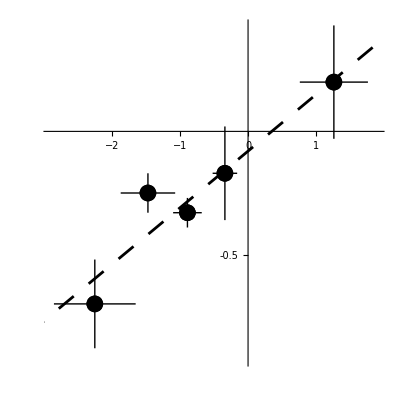

```mathematica
(* REDUCTION IN VISITATION, REDUCTION IN PER CAPITA SEED PRODUCTION *)
Sdata={{-0.89±0.21,-0.33±0.06}};
Bdata={{-1.47±0.40,-0.25±0.08}};
Pdata={{-2.25±0.60,-0.70±0.18}};
Cdata={{-0.34±0.18,-0.17±0.19}};
Ndata={{1.26±0.50,0.20±0.23}};

(* PLOT *)
fig4=Show[(* Best Fit *)Plot[-0.08 + 0.23 x,{x,-6,6},PlotStyle->{Black,Dashing[Large],Thickness[0.005]}],
(* S *)ListPlot[Sdata,PlotStyle->{Black ,PointSize[0.03]}],
(* B *)ListPlot[Bdata,PlotStyle->{Black,PointSize[0.03]}],
(* P *)ListPlot[Pdata,PlotStyle->{Black ,PointSize[0.03]}],
(* C *)ListPlot[Cdata,PlotStyle->{Black,PointSize[0.03]}],
(* N *)ListPlot[Ndata,PlotStyle->{Black ,PointSize[0.03]}],
AspectRatio->1,PlotRange->{{-2.9,1.9},{-0.925,0.425}},AxesOrigin->{0,0},AxesStyle->{Black,Black},Ticks->{Automatic,{-1,{-0.9,""},{-0.8,""},{-0.7,""},{-0.6,""},-0.5,{-0.4,""},{-0.3,""},{-0.2,""},{-0.1,""},{0.1,""},{0.2,""},{0.3,""},{0.4,""},0.5}},LabelStyle->Directive[24]]
```

```mathematica
Export["Fig4.eps",fig4];
```

# Supplementary Analyses

## Supplementary Discussion: effects of competition for pollinators with plants in the broader experimental landscape

## Figure S1a,b: Changes in niche & fitness differences

-Graphics-

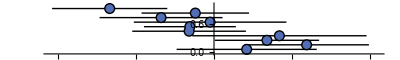

```mathematica
(* Data (S-B, S-P, S-C, S-N, P-B, C-B, B-N, P-C, P-N, C-N; dominant competitor listed first) *)
(* Change in niche differences (x-coordinate: difference, y-coordinate: stacked points) *)
NDdata={{-0.44±0.45,0.95},{-0.31±0.45,0.85},{-0.64±0.48,0.75},{-0.01±0.68,0.65},{-0.74±0.51,0.55},{-0.65±0.54,0.45},{-0.26±0.98,0.35},{-0.25±0.53,0.25},{-0.25±0.75,0.15},{0.83±0.74,0.05}};
(* Change in fitness differences (x-coordinate: difference, y-coordinate: stacked points) *)
FDdata={{-1.34±0.74,0.95},{-0.24±0.69,0.85},{-0.68±0.79,0.75},{-0.05±0.98,0.65},{-0.31±0.59,0.55},{-0.32±0.73,0.45},{0.84±1.12,0.35},{0.68±0.67,0.25},{1.19±0.80,0.15},{0.42±0.90,0.05}};

(* Plots *)
(* Change in niche differences *)
figS1a=Show[ListPlot[NDdata,PlotStyle->{Black},AspectRatio->0.15,PlotRange->{{-2.1,2.1},{-0.05,1.05}},AxesOrigin->{0,-0.05},AxesStyle->{Black,Black},Ticks->{Automatic,None},LabelStyle->{Directive[FontSize->12]}],
ListPlot[NDdata,PlotStyle->{Black,PointSize[0.02]},IntervalMarkersStyle->Transparent],ListPlot[NDdata,PlotStyle->{RGBColor[82/255,110/255,180/255],PointSize[0.015]},IntervalMarkersStyle->Transparent]]

(* Change in fitness differences *)
figS1b=Show[ListPlot[FDdata,PlotStyle->{Black},AspectRatio->0.15,PlotRange->{{-2.1,2.1},{-0.05,1.05}},AxesOrigin->{0,-0.05},AxesStyle->{Black,Black},Ticks->{Automatic,None},LabelStyle->{Directive[FontSize->12]}],
ListPlot[FDdata,PlotStyle->{Black,PointSize[0.02]},IntervalMarkersStyle->Transparent],ListPlot[FDdata,PlotStyle->{RGBColor[82/255,110/255,180/255],PointSize[0.015]},IntervalMarkersStyle->Transparent]]
```

```mathematica
Export["FigS1a.eps",figS1a];
Export["FigS1b.eps",figS1b];
```

## Figure S1c: Niche & Fitness Differences

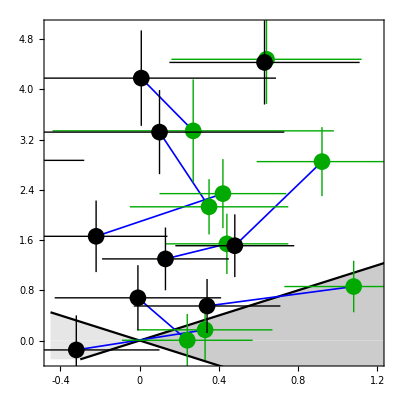

```mathematica
(* Plot parameter space *)
RP=Show[Plot[{-x,x},{x,-0.45,0},Filling->0,FillingStyle->GrayLevel[0.9],PlotStyle->{{Black},{Black}},AxesOrigin->{-0.4,0},PlotRange->{{-0.45,1.2},{-0.3,5}}],Plot[{-x,x},{x,0,1.25},Filling->0,FillingStyle->GrayLevel[0.8],PlotStyle->{{Black},{Black}}],Frame->True,
FrameStyle->{{Black,Black},{Black,Black}},FrameTicks->{{Automatic,None},{{-0.4,0,0.4,0.8,1.2},Automatic}},LabelStyle->Directive[FontSize->20]];

(* Data (Niche difference, fitness difference) *)
hand={(*S-B*){0.92±0.33,2.85±0.55},
(*S-P*){0.44±0.31,1.54±0.48},
(*S-C*){0.42±0.32,2.34±0.55},
(*S-N*){0.64±0.48,4.48±0.71},
(*B-P*){1.08±0.35,0.86±0.41},
(*B-C*){0.33±0.34,0.17±0.48},
(*B-N*){0.27±0.71,3.34±0.82},
(*P-C*){0.24±0.33,0.004±0.42},
(*P-N*){0.35±0.40,2.13±0.44},
(*C-N*){-1.74±0.38,2.45±0.48}};
control={(*S-B*){0.48±0.30,1.51±0.50},
(*S-P*){0.13±0.32,1.30±0.50},
(*S-C*){-0.22±0.36,1.66±0.57},
(*S-N*){0.63±0.48,4.43±0.67},
(*B-P*){0.34±0.37,0.55±0.43},
(*B-C*){-0.32±0.42,-0.15±0.55},
(*B-N*){0.008±0.68,4.18±0.76},
(*P-C*){-0.009±0.42,0.68±0.52},
(*P-N*){0.10±0.63,3.32±0.67},
(*C-N*){-0.91±0.63,2.87±0.76}};
(* End points for arrows (must remove SD) *)
hArrow={(*S-B*){0.92,2.85},
(*S-P*){0.44,1.54},
(*S-C*){0.42,2.34},
(*S-N*){0.64,4.48},
(*B-P*){1.08,0.86},
(*B-C*){0.33,0.17},
(*B-N*){0.27,3.34},
(*P-C*){0.24,0.004},
(*P-N*){0.35,2.13},
(*C-N*){-1.74,2.45}};
cArrow={(*S-B*){0.48,1.51},
(*S-P*){0.13,1.30},
(*S-C*){-0.22,1.66},
(*S-N*){0.63,4.43},
(*B-P*){0.34,0.55},
(*B-C*){-0.32,-0.15},
(*B-N*){0.008,4.18},
(*P-C*){-0.009,0.68},
(*P-N*){0.10,3.32},
(*C-N*){-0.91,2.87}};

(* PLOT PARMAETER SPACE, POINTS, AND ARROWS *)
plot=Show[ListLinePlot[{hArrow[[1]],cArrow[[1]]},PlotMarkers->None,PlotStyle->{Blue,Thickness[0.003]}]/.Line->Arrow,
ListLinePlot[{hArrow[[2]],cArrow[[2]]},PlotMarkers->None,PlotStyle->{Blue,Thickness[0.003]}]/.Line->Arrow,
ListLinePlot[{hArrow[[3]],cArrow[[3]]},PlotMarkers->None,PlotStyle->{Blue,Thickness[0.003]}]/.Line->Arrow,
ListLinePlot[{hArrow[[4]],cArrow[[4]]},PlotMarkers->None,PlotStyle->{Blue,Thickness[0.003]}]/.Line->Arrow,
ListLinePlot[{hArrow[[5]],cArrow[[5]]},PlotMarkers->None,PlotStyle->{Blue,Thickness[0.003]}]/.Line->Arrow,
ListLinePlot[{hArrow[[6]],cArrow[[6]]},PlotMarkers->None,PlotStyle->{Blue,Thickness[0.003]}]/.Line->Arrow,
ListLinePlot[{hArrow[[7]],cArrow[[7]]},PlotMarkers->None,PlotStyle->{Blue,Thickness[0.003]}]/.Line->Arrow,
ListLinePlot[{hArrow[[8]],cArrow[[8]]},PlotMarkers->None,PlotStyle->{Blue,Thickness[0.003]}]/.Line->Arrow,
ListLinePlot[{hArrow[[9]],cArrow[[9]]},PlotMarkers->None,PlotStyle->{Blue,Thickness[0.003]}]/.Line->Arrow,ListPlot[hand,PlotStyle->{Darker[Green],PointSize[0.03],Thin}],ListPlot[control,PlotStyle->{Black,PointSize[0.03],Thin}]];
figS1c=Show[RP,plot,AspectRatio->1]
```

```mathematica
Export["FigS1c.eps",figS1c];
```